# Derivation of p(x|I_1) for J=1

```mathematica
J=n=1;
```

```mathematica
Solve[r==Log[x/c]&&0<c<x,{x},PositiveReals]//FullSimplify
a={c ⅇ^r};
b={r};
J=Det[Grad[a,b]]//FullSimplify
```

{{x→ConditionalExpression[c ⅇ^r,c>0&&r>0]}}

c ⅇ^r

```mathematica
m[u_]:=Exp[u.Join[{0},Range[Length[u]-1]//Reverse]]
m[{r}]
```

1

```mathematica
Z[λ_]:=Integrate[m[{r}] Exp[-{r}.λ],{r,0,∞},Assumptions->λ∈Vectors[1,Reals]&&ρ>0]//FullSimplify
Z[{ρ}]
```

1/ρ

```mathematica
(* Show that ρ is indeed positive, as we assumed in the integral *)
Assuming[ρ>0,D[Log[Z[{ρ}]],{{ρ},1}]==-{mr}]
MEsolution=Solve[%,{mr}][[1]]
```

{-1/ρ}=={-mr}

{mr→1/ρ}

The canonical ME solutions show the (current) constraints on the Lagrange multipliers: ρ>0.

```mathematica
p[u_,λ_]:=(1/Z[λ]) m[u] Exp[-u.λ] (*Boole[AllTrue[u,0<#&]]*)
p[{r},{ρ}]
```

ⅇ^(-r ρ) ρ

```mathematica
Integrate[p[{r},{ρ}],{r,0,∞},Assumptions->ρ>0]
```

1

## Derive joint distribution and marginals

```mathematica
q[x_,c_,ρ_]:=p[{Log[x/c]},{ρ}]/(x) Boole[0<c≤x]
q[x,c,ρ]//FullSimplify
```

((x/c)^-ρ ρ Boole[0<c≤x])/x

```mathematica
Integrate[q[x,c,ρ],{x,-∞,∞},Assumptions->0<c&&ρ>0]
```

1

```mathematica
px[x_,c_,ρ_]:=q[x,c,ρ]
```

For the moments of x to exist, the requirements on the Lagrange multipliers are stricter: ρ>0 now becomes ρ>1.

```mathematica
Ex=Integrate[x px[x,c,ρ],{x,-∞,∞},Assumptions->0<c&&ρ>1]//FullSimplify
```

(c ρ)/(-1+ρ)

## Solve for Lagrange multipliers given formant frequency first moments

It is seen that the solutions automatically enforce the constraints on the Lagrange multipliers that allowed the moments to exist in the first place. This is logical: since we assert the first moments, our ME distribution better allows them to exist. Since these enforced constraints are stricter than those implied by the ME solutions in terms of first moments of u and those necessary for Z(λ) to exist, everything is well-defined.

```mathematica
mcond=0<c<mF1;
```

```mathematica
sol=Refine[Solve[mF1==Ex&&mcond&&ρ>1,{ρ},Reals],Assumptions->mcond][[1]]//FullSimplify
```

{ρ→mF1/(-c+mF1)}

Note that the expression is not symmetric in the ratios: ρ is different from the rest. This can be symmetrized by letting ρ→1+c/(-c+mF1)==mF1/(-c+mF1)

## Plots

Marginals p(x_i|c,μ_(1:i)) are identical for any n≥i given the same information c,μ_(1:i). So indeed knowledge of higher formants does not influence the marginals of lower formant frequencies.

```mathematica
marginals={px[x,c,ρ]}/.sol/.{c->200,mF1->500}//N//FullSimplify
```

{(11399.8 Boole[x≥200.])/x^(8/3)}

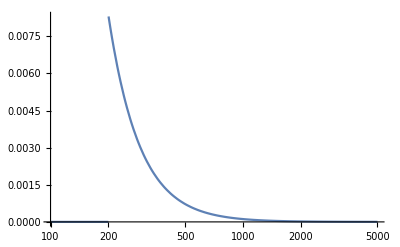

```mathematica
LogLinearPlot[marginals,{x,100,5000},PlotRange->Full]
```